# top26Pc-cited articles (top25~26%)

## 環境設定

```mathematica
(*expordoctdir="/Users/kouamano/gitsrc/pubmed-analysis/202312/"*)
```

```mathematica
expordoctdir="/Volumes/LaCie/BANK/pubmed-analysis/202312/"
```

/Volumes/LaCie/BANK/pubmed-analysis/202312/

## 登録論文数累積

のちの分析のため評価必要。

edgestat-refcount-cumulative.nb より。

```mathematica
artcountAcm={331362,866254,1415896,2141764,3156527,4323230,5675522,7217673,9135438,11279956,13673661,16645203,20421796,25376280,31440632}
```

{331362,866254,1415896,2141764,3156527,4323230,5675522,7217673,9135438,11279956,13673661,16645203,20421796,25376280,31440632}

## 累積世代ごとの高被引用論文(G2)

のちの分析のため評価必要。

### G2論文

```mathematica
top26Pcartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt26Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt26Perc.save}

```mathematica
Map[Get,top26Pcartfiles];
```

主要論文PMIDと被引用数

```mathematica
(top26PcCitedArtList=Table[Reverse[SortBy[Flatten[Map[#[[2]]&,topCitingCitedArt26Perc[n,"citing rule"],{2}]]//Tally,#[[2]]&]],{n,1950,2020,5}])//Length
```

15

```mathematica
Map[#[[2]]&,top26PcCitedArtList,{2}]//Max
Map[#[[2]]&,top26PcCitedArtList,{2}]//Min
```

91

4

全期間のユニークPMID

```mathematica
(top26PcCitedArtPMID=Map[#[[1]]&,top26PcCitedArtList,{2}]//Flatten//Union)//Length
```

89021

```mathematica
numG2=Length[top26PcCitedArtPMID]
```

89021

高被引用論文数

```mathematica
top26PcCitedArtCount=Map[Length,top26PcCitedArtList]
```

{76,305,618,937,1449,2056,2835,3668,4663,5933,7239,9779,14655,19457,25231}

全論文数における高被引用論文数割合（%）

```mathematica
top26pcArtRatio=top26PcCitedArtCount/artcountAcm*100//N
```

{0.0229356,0.0352091,0.0436473,0.043749,0.0459049,0.047557,0.0499514,0.0508197,0.051043,0.0525977,0.0529412,0.0587497,0.0717616,0.076674,0.0802497}

## （調査１）高被引用(G2)論文タイトル

PMIDから論文タイトルを引くルール

プログラム適応

```mathematica
(*(blks=FileNames["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/*blk"])//Length*)
```

```mathematica
(*AbsoluteTiming[(pmidToTitle=Association[Flatten[ParallelMap[blkToTitleRule,blks]]]);]*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save",pmidToTitle]*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle_V2.save",pmidToTitle]*)
```

G2論文タイトル

ルールを読み込む

```mathematica
(*Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save"];*)
```

```mathematica
(*top26pctitle=Map[{pmidToTitle[#[[1]]],#[[2]]}&,top26PcCitedArtList,{2}];*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"top26pctitle.save",top26pctitle]*)
```

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"top26pctitle.save"];
```

## （調査２.１）G2論文のオブソレッセンス（全ての累積世代での出現）

全累積世代に見る論文を候補とする。

```mathematica
top26PcCitedArtPMID//Length
```

89021

### pubyearを調べておく

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/PMIDtoPubyear.wl"];
```

```mathematica
top26PcCitingCitedPMIDvsPY=Map[{#,PMIDtoPubyear[#]}&,top26PcCitedArtPMID];
```

```mathematica
yearlist=Sort[Tally[Map[#[[2]]&,top26PcCitingCitedPMIDvsPY]]]
```

{{1880,1},{1886,1},{1889,1},{1890,1},{1894,3},{1895,1},{1898,2},{1899,1},{1900,1},{1905,1},{1907,1},{1908,1},{1912,2},{1913,5},{1914,2},{1915,3},{1916,3},{1917,3},{1918,1},{1919,3},{1920,2},{1921,5},{1922,2},{1923,5},{1924,3},{1925,5},{1926,6},{1927,7},{1928,8},{1929,10},{1930,5},{1931,15},{1932,21},{1933,24},{1934,21},{1935,20},{1936,21},{1937,29},{1938,35},{1939,30},{1940,38},{1941,51},{1942,48},{1943,55},{1944,64},{1945,98},{1946,106},{1947,107},{1948,125},{1949,188},{1950,414},{1951,569},{1952,523},{1953,526},{1954,487},{1955,539},{1956,612},{1957,633},{1958,754},{1959,667},{1960,605},{1961,601},{1962,641},{1963,663},{1964,722},{1965,656},{1966,722},{1967,698},{1968,809},{1969,812},{1970,900},{1971,894},{1972,885},{1973,841},{1974,995},{1975,1061},{1976,1081},{1977,1133},{1978,1037},{1979,1010},{1980,1033},{1981,1078},{1982,1189},{1983,1159},{1984,1294},{1985,1277},{1986,1336},{1987,1385},{1988,1492},{1989,1519},{1990,1702},{1991,1684},{1992,1789},{1993,1796},{1994,1751},{1995,1832},{1996,1823},{1997,1875},{1998,2085},{1999,2132},{2000,2318},{2001,2337},{2002,2392},{2003,2429},{2004,2604},{2005,2680},{2006,2530},{2007,2467},{2008,2496},{2009,2274},{2010,2224},{2011,1927},{2012,1540},{2013,1240},{2014,945},{2015,637},{2016,494},{2017,306},{2018,162},{2019,51},{2020,55},{2021,1}}

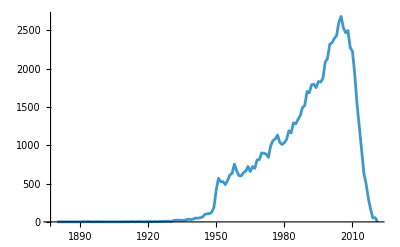

```mathematica
ListPlot[yearlist//ToExpression,PlotRange->Full,Joined->True]
```

### あらためて各論文の被引用の状況を確認する

```mathematica
Map[#[[1]]&,yearlist]//ToExpression//Max
Map[#[[1]]&,yearlist]//ToExpression//Min
```

2021

1880

最も古い高被引用論文は1880出版。

```mathematica
targetYears=Table[ToString[n],{n,1880,2020}]
```

{1880,1881,1882,1883,1884,1885,1886,1887,1888,1889,1890,1891,1892,1893,1894,1895,1896,1897,1898,1899,1900,1901,1902,1903,1904,1905,1906,1907,1908,1909,1910,1911,1912,1913,1914,1915,1916,1917,1918,1919,1920,1921,1922,1923,1924,1925,1926,1927,1928,1929,1930,1931,1932,1933,1934,1935,1936,1937,1938,1939,1940,1941,1942,1943,1944,1945,1946,1947,1948,1949,1950,1951,1952,1953,1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020}

```mathematica
(G2targetCandPMIDvsPY=Map[{#,PMIDtoPubyear[#]}&,top26PcCitedArtPMID])//Length
```

89021

PMIDからタイトルを引く

```mathematica
(*Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save"];*)
```

```mathematica
(*(G2targetCandPMIDvsTitle=Map[{#,pmidToTitle[#]}&,top26PcCitedArtPMID])//Length*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"G2targetCandPMIDvsTitle.save",G2targetCandPMIDvsTitle]*)
```

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"G2targetCandPMIDvsTitle.save"];
```

PMID vs. PMID

```mathematica
(*Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/totalEdge.save"];*)
```

```mathematica
(*AbsoluteTiming[totalEdgeGroupLast=GroupBy[totalEdgeList,Last];]*)
```

```mathematica
(*AbsoluteTiming[(top26PcCitedArtEdges=Map[totalEdgeGroupLast,top26PcCitedArtPMID])//Length]*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/top26PcCitedArtEdges.save",top26PcCitedArtEdges]*)
```

以下はデータ整形

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/top26PcCitedArtEdges.save"];
```

```mathematica
(top26PcCitedArtCitedyear= Map[{PMIDtoPubyear[#[[1]]],{PMIDtoPubyear[#[[2]]],#[[2]]}}&, top26PcCitedArtEdges,{2}])//Length
```

89021

yearごとの被引用数リストを作る

：yearから被引用数を得る

```mathematica
toCitedyearlist[l_]:=Module[{citedPMID},
citedPMID=l[[1,2]];
{citedPMID,Association[MapApply[Rule,Tally[Map[#[[1]]&,l]]]]}
]
```

```mathematica
(top26PcCitedArtCitedyearAssociations=Map[toCitedyearlist,top26PcCitedArtCitedyear])//Length
```

89021

：1880からの被引用数リストにする

```mathematica
fromAscToCount[asc_,year_]:=Map[asc[#]&,year]/.{_Missing->0}
```

<1880からの累積被引用数リスト>

```mathematica
(top26PcCitedArtCitedCount["1880-2020"]=Map[{#[[1]],fromAscToCount[#[[2]],targetYears]}&,top26PcCitedArtCitedyearAssociations])//Length
```

89021

：出版年からの被引用数リストにする

```mathematica
fromPY[l_,y_]:=Module[{py,pyp},
py=l[[1,1]];
pyp=Flatten[Position[y,py]][[1]];
{l[[1]],l[[2]][[pyp;;]]}
]
```

```mathematica
(top26PcCitedArtCitedCount["PY-2020"]=Map[fromPY[#,targetYears]&,top26PcCitedArtCitedCount["1880-2020"]])//Length
```

Part::partw: {}の部分1は存在しません．

Part::span: {}⟦1⟧;;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

89021

### 分析

#### plot用カラー/サイズ定義

以下はplotの色の調整

```mathematica
myColor1[z_]:=RGBColor[z,0.8(1-z),0.4(1-z)];
myColor2[z_]:=CMYKColor[z,((1-z)/3)^2,((1-z)/2)^2,Sqrt[z]];
myColor3[z_]:=CMYKColor[((1-z)/3)^2,z,((1-z)/2)^2,Sqrt[z]];
myColor4[z_]:=CMYKColor[((1-z)/3)^2,((1-z)/3)^2,z,Sqrt[z]];
myColor5[z_]:=CMYKColor[(z)^2,(z),(z),(z)^(1.2)];
myColor6[z_]:=Blend[{Red,Green,White},{1,0.75(1-z),(1-z)^(3)}];
cf1=Function[{x,y,z},Hue[5/6 (1-z),0.3+(z^2),1]];
cf2=Function[{x,y,z},Hue[5/6 (1-z),#+(1-#)*z,1]&@0.05];
cf3=Function[{x,y,z},Hue[5/6*(1-z),(#1+(1-#1)*z)^#2,1]]&@@{.25(*offset*),1.0(*gain*)};
```

```mathematica
imsz1=260
imsz2=320
imsz3=480
imsz4=540
```

260

320

480

540

#### 指標値

オブソレッセンスベクトル = O(Gs,A-)：Sunらの論文より、指標 "Gs" と "A-" の定義：
Gs = 1 - ((2 [n*c1 + (n-1)*c2 + ...] - C) / (C*n)); n:age, c:year cited, C:total cited;
A = “A-” + “A+”;
B : year accumulation (normarized).
"A-"、"A+"にかかる定義文（和訳）:「したがって、値が正となる A+ を、平等線（完全平等線）と、その平等線より下にある正規化曲線との間の面積として定義し、値が負となる A− を、平等線と、その平等線より上にある正規化曲線との間の面積として定義する。」
このとき、オブソレッセンスベクトルは : (Gs,”A-”)

```mathematica
Gsf[l_]:=Module[{len,Ct,Yr},
len=Length[l];
Ct=Total[l];
Yr=Reverse[Table[n,{n,Length[l]}]];
If[Ct==0,1,1-((2 Total[Yr * l]-Ct) / (len * Ct))]
]
```

```mathematica
obsGs[l_]:=Module[{ac,acR,ht,len,area,A,Gs,Ang,Ap,normstep,normseq,Aseq},
ac=Accumulate[l]//N;
ht=Last[ac];
len=Length[ac];
area=ht*len;
acR=ac/area;
normstep=Last[acR]/len;
normseq=Table[normstep*n,{n,len}];
Aseq=normseq-acR;
A=Total[Aseq];
Ang=Cases[Aseq,x_/;x<0]//Total;
Ap=Cases[Aseq,x_/;x>0]//Total;
Gs=Gsf[l]//N;
Association[{"Gs"->Gs,"A-"->Ang,"A+"->Ap,"A"->A,"len"->len}]
]
```

```mathematica
obsGsseq[l_]:=Table[obsGs[Take[l,n]],{n,Length[l]}]
```

その他の主要指標：

"len" => 出版から2020までの年数
“peakYear” => 出版からピークを迎えるまでの年数☑️
“peakCount” => ピークの年の被引用数☑️
“peakRatio” => peakCount/decayCited（”活動期間”の被引用）
“peakPosition” => “活動期間”中におけるpeakの位置（全体を1とする）
“sustainYear” => ピークの年から2020までの年数
“acR” => last cited / accumulate cited
“decayYear” => ピークの年を超えてから年間引用が全体の引用の5%以下となるまでの出版からの年数☑️
“decayCited” => decayYearまでの被引用数☑️
“firstCitedYear” => 最初の引用が発生するまでの年数（出版年に発生すると0）
“totalCited” => 出版年から2020までの総被引用数
“V:Av5year” => 5年引用数平均の分散☑️
“V:diff” => 5年引用数平均の差分の分散（ゼロパディングあり=>出版年での立ち上がりが見える）☑️
“V:diff2” => 5年引用数平均の差分の差分の分散☑️
“diffTotal” => 5年引用数平均の差分の累計：十分に大きい値があり十分に長い期間があれば0に近づく

```mathematica
acRatio[l_]:=Module[{ac},
ac=Accumulate[l];
N[l/ac]/.Indeterminate->1
]
```

```mathematica
ndiff[l_,w_]:=BlockMap[(#[[-1]]-#[[1]])/(w-1)&,Join[Table[0,{w-1}],l],w,1]
```

```mathematica
ndiff[l_]:=BlockMap[(#[[-1]]-#[[1]])&,l,2,1]
```

```mathematica
myVar[l_]:=If[Length[l]>1,Variance[l],0]
```

```mathematica
basicStat[citedcount_]:=Module[{len,argPeak,peakYear,max,sustainYear,decayTH,acR,decayPlist,decayCited,decayPeriod,firstCitedYear,total,Av5year,diff,diff2,diffTotal},
decayTH=0.05;
len=Length[citedcount];
argPeak=Flatten[Position[citedcount,max=Max[citedcount]]];
peakYear=argPeak[[1]];
sustainYear=len-argPeak[[-1]];
acR=acRatio[citedcount];
decayPlist=Cases[Flatten[Position[acRatio[citedcount],x_/;x<=decayTH]],x_/;x>peakYear];
decayCited=Total[citedcount[[;;Min[decayPlist]]]];
decayPeriod=Min[decayPlist]-peakYear;
If[Length[decayPlist]<=0,decayPeriod="InDecay"];
firstCitedYear=Min[Position[citedcount,x_/;x>0]]-1;
total=Total[citedcount];
Av5year=MovingAverage[Join[citedcount,Table[0,{n,4}]],5];
diff=ndiff[Av5year];
diff2=ndiff[diff];
diffTotal=Total[diff//N];
Association[{"len"->len,"peakYear"->peakYear,"peakCount"->max,"peakRatio"->max/decayCited//N,"acRatio"->acR,"peakPosition"->peakYear/Min[decayPlist]//N,"sustainYear"->sustainYear,"decayCited"->decayCited,"decayPeriod"->decayPeriod,"firstCitedYear"->firstCitedYear,"totalCited"->total,"V:Av5year"->myVar[Av5year//N],"V:diff"->myVar[diff//N],"V:diff2"->myVar[diff2//N],"diffTotal"->diffTotal,"diffSeq"->diff}]
]
```

```mathematica
toItemNormarizeMat[l_]:=Module[{m,key},
key=Keys[l[[1,2]]];
m=Map[Normal[#[[2]]]&,l]/.{None->0};
Transpose[Map[Normalize,Transpose[Map[#[[2]]&,m,{2}]]]//N]
]
```

```mathematica
totalize[l_]:=l/Total[l]
```

```mathematica
(G2bs=Map[{#[[1]],basicStat[#[[2]]]}&,top26PcCitedArtCitedCount["PY-2020"]])//Length
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

Part::span: 1;;∞は有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

General::stop: この計算中に，Part::spanのこれ以上の出力は表示されません．

Part::partw: {}の部分1は存在しません．

Part::partw: {}の部分-1は存在しません．

Part::pkspec1: 式{{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,«13»,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,«91»}は部分指定に使用できません．

Join::heads: 位置1と2での頭部PartとListは等しいことが想定されています．

MovingAverage::vecmat: 位置1の引数Join[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«91»}⟦{}⟦1⟧;;All⟧,{0,0,0,0}]が非空のベクトルでも非空の行列でもありません．

Join::heads: 位置1と2での頭部PartとListは等しいことが想定されています．

General::stop: この計算中に，Join::headsのこれ以上の出力は表示されません．

MovingAverage::vecmat: 位置1の引数Join[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«91»}⟦{}⟦1⟧;;All⟧,{0.,0.,0.,0.}]が非空のベクトルでも非空の行列でもありません．

General::stop: この計算中に，MovingAverage::vecmatのこれ以上の出力は表示されません．

89021

```mathematica
(G2obsIdx=Map[obsGsseq[#[[2]]]&,top26PcCitedArtCitedCount["PY-2020"]])//Dimensions
```

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Part::span: {}⟦1⟧;;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

Part::pkspec1: 式{{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,«13»,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,«91»}は部分指定に使用できません．

Thread::tdlen: {({0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«3»,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«91»}⟦{«1»}⟧)/(4 (89+Part[«2»];;All)),({0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«31»,0.,0.,0.,0.,0.,0.,0.,0.,0.,«91»}⟦{«1»}⟧)/(2 (89+Part[«2»];;All))}+{-({0.,0.,0.,«46»,0.,«91»}⟦{«1»}⟧)/(2 ({}⟦1⟧;;All)),-(«1»)/(2 «1»),«47»,-(«1»)/(«1»),«91»}の長さが異なるオブジェクトは結合することができません．

Part::span: {}⟦1⟧;;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

{89021}

#### オブソレッセンスベクトルの確認

Sunらの論文の指標、O(Gs, A-)の算出。

```mathematica
Map[#["len"]&,Map[Last,G2obsIdx]]//Max
Map[#["len"]&,Map[Last,G2obsIdx]]//Min
```

141

1

```mathematica
(G2obsGs=Map[#["Gs"]&,Map[Last,G2obsIdx]])//Dimensions
(G2obsAng=Map[#["A-"]&,Map[Last,G2obsIdx]])//Dimensions
(G2obsAp=Map[#["A+"]&,Map[Last,G2obsIdx]])//Dimensions
(G2obsA=Map[{#["Gs"],#["A"]}&,Map[Last,G2obsIdx]])//Dimensions
(G2obsAA=Map[{#["A-"],#["A+"],#["Gs"]}&,Map[Last,G2obsIdx]])//Dimensions
(G2obsVec=Map[{#["Gs"],#["A-"]}&,Map[Last,G2obsIdx]])//Dimensions
(G2obsVecP=Map[{#["Gs"],#["A+"]}&,Map[Last,G2obsIdx]])//Dimensions
(G2obsSpec3D=Map[{#["Gs"],#["A-"],#["len"]}&,Map[Last[#]&,G2obsIdx]])//Dimensions
(G2obsA3D=Map[{#["A-"],#["A+"],#["len"]}&,Map[Last[#]&,G2obsIdx]])//Dimensions
```

{89021}

{89021}

{89021}

{89021,2}

{89021,3}

{89021,2}

{89021,2}

{89021,3}

{89021,3}

・引用ピークが早期であるほど "Gs" が小さくなる。
・オブソレッセンス状態にあるほど”A-”が小さくなる傾向にある。

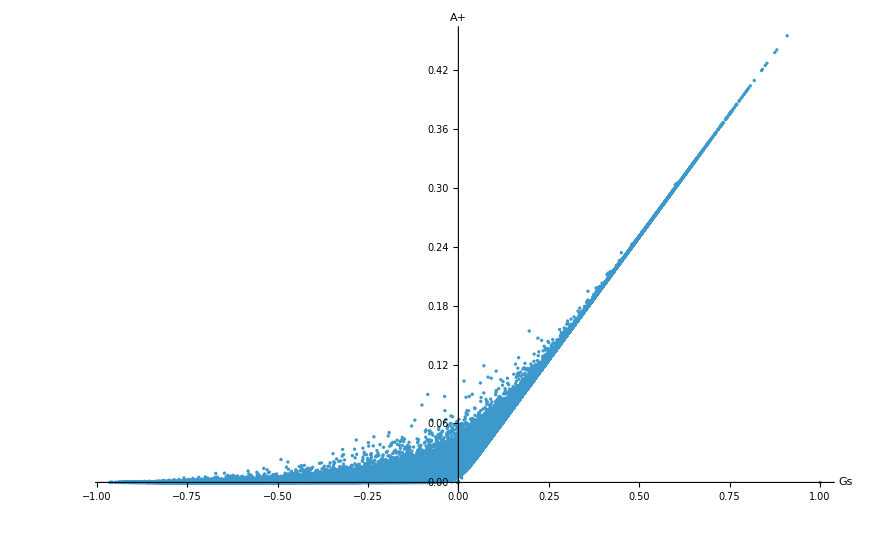

```mathematica
(*ListPlot[G2obsVecP,PlotRange->Full,AxesLabel->{Text[Style["Gs",20]],Text[Style["A+",20]]}]*)
```

```mathematica
(*ListPointPlot3D[G2obsSpec3D,Filling->Bottom,AxesLabel->{"Gs","A-","year"}]*)
```

-Graphics3D-

#### Flash in the pan と Sleeping beauty、その他

Sunらの論文の指標、Gs、A- 、A+をを使い、Flash in the pan と Sleeping beauty の存在を確認する。

Paroloらの論文の報告 （ピーク年） とも比較する。（概ねどの分野も2~7年で被引用ピークを迎える）

```mathematica
binMaxPosition[l_,{min_,max_,step_}]:=Module[{span,BC,maxV,maxP},
span=Table[n,{n,min,max,step}];
BC=BinCounts[l,{min,max,step}];
maxV=Max[BC];
maxP=Position[BC,maxV]//Flatten;
(*{span,BC,maxV,maxP,{span[[maxP]],span[[maxP]]+step}};*)
{maxV,maxP,span[[maxP]],span[[maxP]]+step}
]
```

瓶幅：3

```mathematica
binW=3
```

3

FP; Flash in the pan

Gsが小さい Gs < -0.6

A-が小さい A- < - 0.3

```mathematica
(G2obsFP=Position[G2obsVec,{x_,y_}/;x<-0.6&&y<-0.3]//Flatten)//Length
```

11254

中央値：

```mathematica
G2medV["FP"]=G2obsAA[[G2obsFP]]//Median
```

{-0.347324,0.000287274,-0.69375}

```mathematica
G2len["FP"]=Map[#[[3]]&,G2obsA3D[[G2obsFP]]]//Median
```

51

Nm; 通常（対数正規分布）型

Gs: -0.6 <= Gs >= 0.6

A+の値を持つ: A+ > 0

A-の値を持つ: A- < 0

|A-| > |A+|

```mathematica
(G2obsNm=Position[G2obsAA,{ang_,ap_,gs_}/;gs>=-0.6&&gs<=0.6&&ang<0&&ap>0&&Abs[ang]>Abs[ap]]//Flatten)//Length
```

36575

中央値：

```mathematica
G2medV["Nm"]=G2obsAA[[G2obsNm]]//Median
```

{-0.119364,0.00242664,-0.231429}

```mathematica
G2len["Nm"]=Map[#[[3]]&,G2obsA3D[[G2obsNm]]]//Median
```

32

No; 通常型かつオブソレッセンス状態

Gs: -0.6 <= Gs >= 0.6

A+の値を持つ: A+ > 0

A-の値を持つ: A- < -0.1

|A-| > |A+|

```mathematica
(G2obsCmp=Position[G2obsAA,{ang_,ap_,gs_}/;gs>=-0.6&&gs<=0.6&&ang<-0.1&&ap>0&&Abs[ang]>Abs[ap]]//Flatten)//Length
```

20634

```mathematica
G2medV["No"]=G2obsAA[[G2obsCmp]]//Median
```

{-0.197542,0.00111111,-0.391667}

```mathematica
G2len["No"]=Map[#[[3]]&,G2obsA3D[[G2obsCmp]]]//Median//N
```

40.

```mathematica
Map[#[[2]]["peakYear"]&,G2bs[[G2obsCmp]]]//Median
```

5

SB; Sleeping beauty(1)

Gsが大きい Gs > 0.6

A+が大きい A+ > 0.3

```mathematica
(G2obsSB=Position[G2obsVecP,{x_,y_}/;x>0.6&&y>0.3]//Flatten)//Length
```

301

中央値：

```mathematica
G2medV["SB"]=G2obsAA[[G2obsSB]]//Median
```

{0,0.32381,0.647619}

```mathematica
G2len["SB"]=Map[#[[3]]&,G2obsA3D[[G2obsSB]]]//Median//N
```

42.

O; いずれにも分類されなかったもの

```mathematica
(G2obsOthers=Complement[Table[n,{n,numG2}],Join[G2obsFP,G2obsSB,G2obsNm]])//Length
```

40891

中央値：

```mathematica
G2medV["O"]=(G2obsAA[[G2obsOthers]]/.If[___]->0//Median)
```

If::argbu: Ifは1つの引数で呼ばれました．2個から4個の引数が想定されています．

{-0.000897989,0.0740741,0.14249}

```mathematica
G2len["O"]=Map[#[[3]]&,G2obsA3D[[G2obsOthers]]]//Median//N
```

19.

表：

項目

```mathematica
G2medV["head"]={"A^-","A^+","Gs"}
```

{A^-,A^+,Gs}

メンバー数

```mathematica
G2Nmem={11254,36575,20634,301,40891}
```

{11254,36575,20634,301,40891}

```mathematica
G2Pcmem=Round[G2Nmem/numG2*100]
```

{13,41,23,0,46}

年齢

```mathematica
G2Nlen={G2len["FP"],G2len["Nm"],G2len["No"],G2len["SB"],G2len["O"]}
```

{51,32,40.,42.,19.}

```mathematica
Append[Append[Prepend[Transpose[Prepend[Round[{G2medV["FP"],G2medV["Nm"],G2medV["No"],G2medV["SB"],G2medV["O"]},0.001],G2medV["head"]]],{"クラス","FP","Nm","No","SB","O"}],{"年齢",51.,32.,40.,42.,19.}],{"メンバー数\n(%:G1との比較)","11254(13↑)","36575(41↑)","20634(23↑)","301(0↓)","40891(46↓)"}]//Transpose//TableForm
```

クラス | A^- | A^+ | Gs | 年齢 | メンバー数
(%:G1との比較)
FP | -0.347 | 0. | -0.694 | 51. | 11254(13↑)
Nm | -0.119 | 0.002 | -0.231 | 32. | 36575(41↑)
No | -0.198 | 0.001 | -0.392 | 40. | 20634(23↑)
SB | 0. | 0.324 | 0.648 | 42. | 301(0↓)
O | -0.001 | 0.074 | 0.142 | 19. | 40891(46↓)